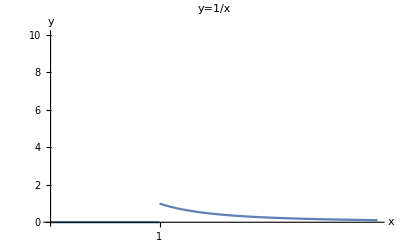

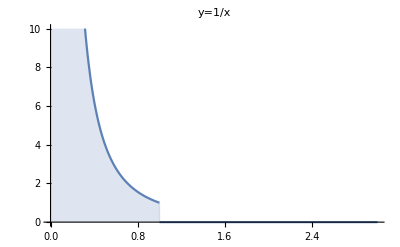

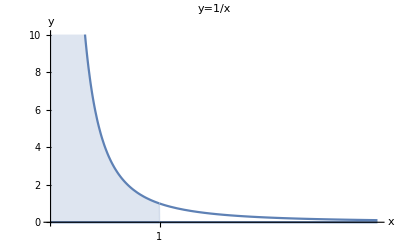

```mathematica
a=Plot[Piecewise[{{1/x^2,x>1},{0,0<x<1}}],{x,0,3},PlotRange->{0,10},AxesLabel->{x,y},Ticks->{{1},None},PlotLabel->"y=1/x"]
b=Plot[Piecewise[{{1/x^2,0<x<1},{0,x>1}}],{x,0,3},Filling->Axis,PlotRange->{0,10},PlotLabel->"y=1/x"]
Show[a,b]
```

```mathematica
RowReduce[{{3,6,1},{2,4,1},{1,2,1},{-1,-2,2}}]
MatrixForm[%]
```

{{1,2,0},{0,0,1},{0,0,0},{0,0,0}}

(1 | 2 | 0
0 | 0 | 1
0 | 0 | 0
0 | 0 | 0)